## Interraction of two bar magnets

```mathematica
Fmagn[x_]:= (B0^2 A^2(L^2+R^2))/(π μ0 L^2)(1/x^2+1/(x+2L)^2-2/(x+L)^2)
```

```mathematica
μ0 = 1.26*10^-6;
B0 = 10^-0;
R = 0.01;
A = π R^2;
L = 0.1;
```

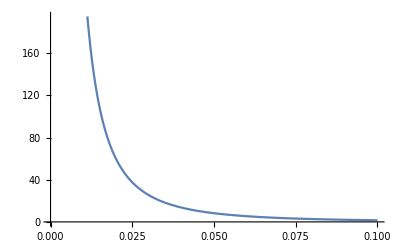

```mathematica
Plot[Fmagn[x],{x, 0, 0.1}]
```

## Force of a leaf spring

-Graphics-

q1 = 4 for rectangular spring

-Graphics-

```mathematica
Fspring[s_]:=(b Em h^3 s)/(Ls^3 4)
```

```mathematica
Ls = 1;
h = 0.2*10^-3;
b=2*10^2;
Em = 2*10^11;
```

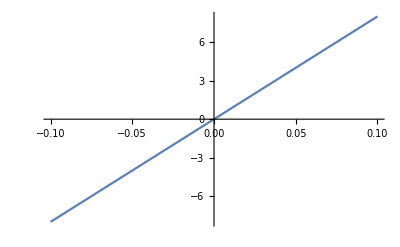

```mathematica
Plot[Fspring[x], {x, -0.1, 0.1}]
```

```mathematica
xLeft0 = 0;
xRight0 = 0.1;
mLeft = 10^-2;
mRight = 10^-2;
```

```mathematica
solution = NDSolve[{xLeft[0] == xLeft0, xRight[0] == xRight0, xRight'[0] == -3, xLeft'[0] == -3,
xRight''[t] == -Fspring[xRight[t]-xRight0]/mRight+ Fmagn[xRight[t] - xLeft[t]]/mRight, 
xLeft''[t] == -Fspring[xLeft[t]-xLeft0]/mLeft-Fmagn[xRight[t] - xLeft[t]]/mLeft},
 {xLeft[t], xRight[t]},{t, 0, 10}]
```

{{xLeft[t]→InterpolatingFunction[…][t],xRight[t]→InterpolatingFunction[…][t]}}

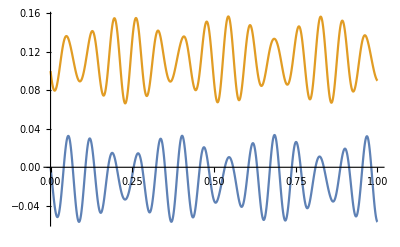

```mathematica
Plot[{solution[[1,1, 2]], solution[[1,2, 2]]}, {t, 0, 1}]
```